# Force-free fields and their stability

## Linear force-free solutions in spherical geometry

Stationary states are solutions of the linear force-free equation ∇×B=λ B, where λ is a constant throughout the space. The general solutions are in the form B=r×∇χ+1/λ∇×(r×∇χ), where χ satisfies the scalar Helmholtz equation ∇^2 χ+λ^2 χ=0. In spherical coordinate, χ=j_l(λ r)Y_(l m)(θ,ϕ) in general (j_l is spherical Bessel function and Y_(l m) is spherical harmonic). If the boundary is a spherical, perfectly conducting wall with radius R, the boundary condition would be B_r(r=R)=0, so only a particular l can present, and λR should be the n-th zero of the spherical Bessel function j_l(x). Now we specify a solution by the three numbers: l, m, n.

Here are flux surfaces of a few m=0 solutions on the meridional plane (λ=1 in the following examples). In the following figures, the stream lines show the field component parallel to the plane and color shows the component perpendicular to the plane.

### l=1, m=0

Expression of B in spherical representation is (B={B_r, B_θ, B_ϕ}):

```mathematica
B[r_,θ_,ϕ_]:={(√(3/π) Cos[θ] (r Cos[r]-Sin[r]))/r^3,1/(2 r^3)√(3/π) (r Cos[r]+(-1+r^2) Sin[r]) Sin[θ],(√(3/π) (r Cos[r]-Sin[r]) Sin[θ])/(2 r^2)};
```

First isolating surface at

```mathematica
r1=BesselJZero[1+1/2,1]//N
```

4.49341

Second isolating surface

```mathematica
r2=BesselJZero[1+1/2,2]//N
```

7.72525

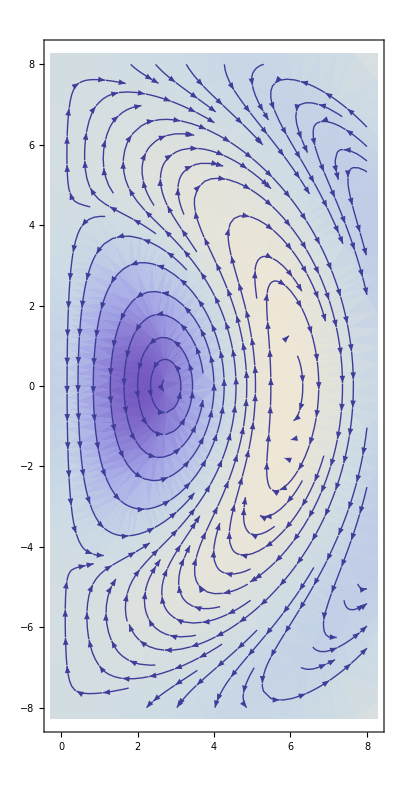

```mathematica
StreamDensityPlot[Evaluate[{{B[r,θ,ϕ][[1]]Sin[θ]+B[r,θ,ϕ][[2]]Cos[θ],B[r,θ,ϕ][[1]]Cos[θ]-B[r,θ,ϕ][[2]]Sin[θ]},B[r,θ,ϕ][[3]]}/.{r->√(x^2+z^2),θ->ArcCos[z/(√(x^2+z^2))],ϕ->0}],{x,0,8},{z,-8,8},AspectRatio->2]
```

### l=2, m=0

```mathematica
B[r_,θ_,ϕ_]:={1/(4 r^4)3 √(5/π) (1+3 Cos[2 θ]) (3 r Cos[r]+(-3+r^2) Sin[r]),-1/(2 r^4)3 √(5/π) Cos[θ] (r (-6+r^2) Cos[r]-3 (-2+r^2) Sin[r]) Sin[θ],1/(2 r^3)3 √(5/π) Cos[θ] (3 r Cos[r]+(-3+r^2) Sin[r]) Sin[θ]};
```

First isolating surface at

```mathematica
r1=BesselJZero[2+1/2,1]//N
```

5.76346

Second isolating surface

```mathematica
r2=BesselJZero[2+1/2,2]//N
```

9.09501

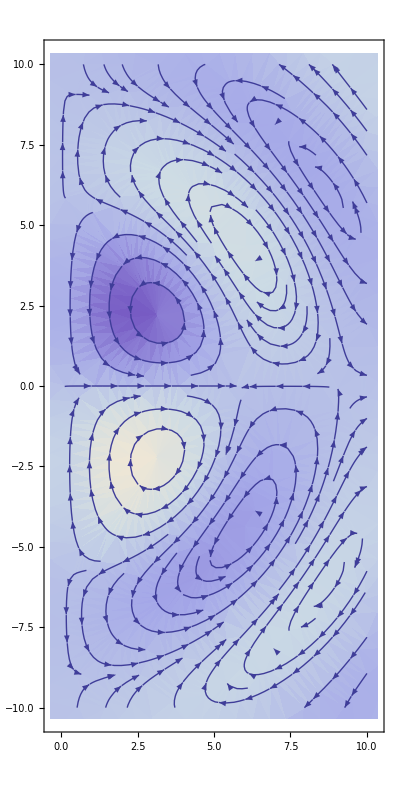

```mathematica
StreamDensityPlot[Evaluate[{{B[r,θ,ϕ][[1]]Sin[θ]+B[r,θ,ϕ][[2]]Cos[θ],B[r,θ,ϕ][[1]]Cos[θ]-B[r,θ,ϕ][[2]]Sin[θ]},B[r,θ,ϕ][[3]]}/.{r->√(x^2+z^2),θ->ArcCos[z/(√(x^2+z^2))],ϕ->0}],{x,0,10},{z,-10,10},AspectRatio->2]
```

## Instability of an example: l=1, m=0

Here for simplicity, assume the boundary is a fixed, spherical, perfectly conducting wall. As an example, we look at the solutions with l=1, m=0, n arbitrary.

```mathematica
B[r_,θ_,ϕ_]:={(√(3/π) Cos[θ] (r Cos[r]-Sin[r]))/r^3,(√(3/π) (r Cos[r]+(-1+r^2) Sin[r]) Sin[θ])/(2 r^3),(√(3/π) (r Cos[r]-Sin[r]) Sin[θ])/(2 r^2)}
```

Under this boundary condition, we require B_n=0 and ξ_n=0. So a perturbation ξ⃗ leads to a change in the potential energy

δW = ∫d^3 r{[∇×(ξ×B)]^2-λ(ξ×B)·[∇×(ξ×B)]}

We generate the trial functions in the following way: let χ_1=f(r)Y_10(θ,ϕ), χ_2=g(r)Y_10(θ,ϕ), then take ξ⃗=a r̂×∇χ_1+b∇×( r̂×∇χ_1)+c ∇χ_2. For simplicity, we let f(r)=d_1 Sin (π r/R)+d_2 Sin (2π r/R)+d_3 Sin (3π r/R), g(r)=h_1 Sin (π r/R/2)+h_2 Sin (3π r/R/2)+h_3 Sin (5π r/R/2): these choices make sure that ξ_n=0 on the boundary and ξ is regular inside the region. (I think the component parallel to B does not matter.) Now we minimize δW under the constraint ∫d^3 (r(ξ×B))^2=1 and get the coefficients {a, b, c, d_1,d_2, d_3, h_1, h_2, h_3}.

#### Codes

```mathematica
<<"VectorAnalysis`"
SetCoordinates[Spherical[r,θ,ϕ]];
```

```mathematica
B[r_,θ_,ϕ_]:={(√(3/π) Cos[θ] (r Cos[r]-Sin[r]))/r^3,(√(3/π) (r Cos[r]+(-1+r^2) Sin[r]) Sin[θ])/(2 r^3),(√(3/π) (r Cos[r]-Sin[r]) Sin[θ])/(2 r^2)}
```

```mathematica
r1=N[BesselJZero[1/2+1,1],30]
```

4.49340945790906417530788092728

```mathematica
r2=N[BesselJZero[1+1/2,2],30]
```

7.72525183693770716419506893306

```mathematica
r3=N[BesselJZero[1+1/2,3],30]
```

10.9041216594288998271487027902

```mathematica
Clear[f,g]
```

```mathematica
χ1=FullSimplify[f[r](SphericalHarmonicY[l,m,θ,ϕ]+SphericalHarmonicY[l,-m,θ,ϕ])/2/.{l->1,m->0}]
```

1/2 √(3/π) Cos[θ] f[r]

```mathematica
ξ1=Simplify[{r,0,0}×Grad[χ1]]
```

{0,0,-1/2 √(3/π) f[r] Sin[θ]}

```mathematica
ξ2=Simplify[Curl[{r,0,0}×Grad[χ1]]]
```

{-(√(3/π) Cos[θ] f[r])/r,(√(3/π) Sin[θ] (f[r]+r f'[r]))/(2 r),0}

```mathematica
χ2=g[r]SphericalHarmonicY[l,m,θ,ϕ]/.{l->1,m->0};
ξp=Grad[χ2]
```

{1/2 √(3/π) Cos[θ] g'[r],-(√(3/π) g[r] Sin[θ])/(2 r),0}

```mathematica
ξ=Simplify[a ξ1+b ξ2 +c ξp]
```

{(√(3/π) Cos[θ] (-2 b f[r]+c r g'[r]))/(2 r),(√(3/π) Sin[θ] (b f[r]-c g[r]+b r f'[r]))/(2 r),-1/2 a √(3/π) f[r] Sin[θ]}

```mathematica
A1=Simplify[ξ×B[r,θ,ϕ]]
```

{(3 Sin[θ]^2 (f[r] ((a+b) r Cos[r]-(a+b-a r^2) Sin[r])+(r Cos[r]-Sin[r]) (-c g[r]+b r f'[r])))/(4 π r^3),-(3 Cos[θ] (r Cos[r]-Sin[r]) Sin[θ] (2 (a-b) f[r]+c r g'[r]))/(4 π r^3),1/(8 π r^4)3 Sin[2 θ] (2 c g[r] (r Cos[r]-Sin[r])-2 b f[r] (2 r Cos[r]+(-2+r^2) Sin[r])+r (-2 b (r Cos[r]-Sin[r]) f'[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g'[r]))}

```mathematica
B1=Simplify[Curl[A1]]
```

{1/(8 π r^5)3 (1+3 Cos[2 θ]) (2 c g[r] (r Cos[r]-Sin[r])-2 b f[r] (2 r Cos[r]+(-2+r^2) Sin[r])+r (-2 b (r Cos[r]-Sin[r]) f'[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g'[r])),1/(8 π r^5)3 Sin[2 θ] (2 c g[r] (3 r Cos[r]+(-3+r^2) Sin[r])+2 b f[r] (r (-6+r^2) Cos[r]-3 (-2+r^2) Sin[r])-r^2 (c r (r Cos[r]-Sin[r]) g'[r]-2 b (r Cos[r]-Sin[r]) f''[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g''[r])),1/(8 π r^4)3 Sin[2 θ] (2 c g[r] (r Cos[r]-Sin[r])+2 f[r] ((a-3 b) r Cos[r]-(a+b (-3+r^2)) Sin[r])+r (-2 a (r Cos[r]-Sin[r]) f'[r]+c ((r Cos[r]+(-1+r^2) Sin[r]) g'[r]+r (-r Cos[r]+Sin[r]) g''[r])))}

```mathematica
du=Simplify[B1.(B1-A1)]
```

1/(64 π^2 r^10)9 ((1+3 Cos[2 θ]) (2 c g[r] (r Cos[r]-Sin[r])-2 b f[r] (2 r Cos[r]+(-2+r^2) Sin[r])+r (-2 b (r Cos[r]-Sin[r]) f'[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g'[r])) (-2 r^2 Sin[θ]^2 (f[r] ((a+b) r Cos[r]-(a+b-a r^2) Sin[r])+(r Cos[r]-Sin[r]) (-c g[r]+b r f'[r]))+(1+3 Cos[2 θ]) (2 c g[r] (r Cos[r]-Sin[r])-2 b f[r] (2 r Cos[r]+(-2+r^2) Sin[r])+r (-2 b (r Cos[r]-Sin[r]) f'[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g'[r])))+Sin[2 θ]^2 (-2 c g[r] (3 r Cos[r]+(-3+r^2) Sin[r])+2 f[r] (r (6 b-a r^2) Cos[r]+(a r^2+2 b (-3+r^2)) Sin[r])+r^2 (-2 b (r Cos[r]-Sin[r]) f''[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g''[r])) (-2 c g[r] (3 r Cos[r]+(-3+r^2) Sin[r])-2 b f[r] (r (-6+r^2) Cos[r]-3 (-2+r^2) Sin[r])+r^2 (c r (r Cos[r]-Sin[r]) g'[r]-2 b (r Cos[r]-Sin[r]) f''[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g''[r]))+r^2 (r Cos[r]-Sin[r]) Sin[2 θ]^2 (-2 (a-b) f[r]+r (2 (a-b) f'[r]+c r g''[r])) (-2 c g[r] (r Cos[r]-Sin[r])+f[r] (-2 (a-3 b) r Cos[r]+2 (a+b (-3+r^2)) Sin[r])-r (-2 a (r Cos[r]-Sin[r]) f'[r]+c ((r Cos[r]+(-1+r^2) Sin[r]) g'[r]+r (-r Cos[r]+Sin[r]) g''[r]))))

```mathematica
dur=Simplify[Integrate[2π du r^2 Sin[θ],{θ,0,π}]]
```

```mathematica
dur=-1/(20 π r^8)3 (4 c^2 g[r]^2 (-15-8 r^2+(15-22 r^2+2 r^4) Cos[2 r]+(30 r-8 r^3) Sin[2 r])+4 f[r]^2 (-60 b^2-a^2 r^2+12 a b r^2-7 b^2 r^2-a^2 r^4+5 a b r^4-7 b^2 r^4+(-a^2 r^2 (-1+r^2)+a b r^2 (-12+19 r^2-2 r^4)+b^2 (60-113 r^2+17 r^4)) Cos[2 r]+2 r (a^2 r^2+4 a b r^2 (-3+r^2)+b^2 (60-29 r^2+r^4)) Sin[2 r])+2 c r g[r] (4 (a r^2-3 b (-4+r^2)) (-r Cos[r]+Sin[r])^2 f'[r]+2 c (-6+2 r^2+r^4+(6-14 r^2+3 r^4) Cos[2 r]+r (12-10 r^2+r^4) Sin[2 r]) g'[r]-r (4 b (3+2 r^2+(-3+4 r^2) Cos[2 r]+r (-6+r^2) Sin[2 r]) f''[r]+c (-6+r^2-3 r^4+(6-13 r^2+r^4) Cos[2 r]-6 r (-2+r^2) Sin[2 r]) g''[r]))+r^2 (8 (-a^2 r^2+a b r^2+b^2 (-6+r^2)) (-r Cos[r]+Sin[r])^2 f'[r]^2-12 c^2 (r Cos[r]+(-1+r^2) Sin[r])^2 g'[r]^2+4 b c r^3 (-r Cos[r]+Sin[r])^2 g'[r] f''[r]+4 c (r Cos[r]-Sin[r]) f'[r] ((a r^2-2 b (-6+r^2)) (r Cos[r]+(-1+r^2) Sin[r]) g'[r]-(2 a-b) r^3 (r Cos[r]-Sin[r]) g''[r])+r^2 (-8 b^2 (-r Cos[r]+Sin[r])^2 f''[r]^2+4 b c (1+(-1+2 r^2) Cos[2 r]+r (-2+r^2) Sin[2 r]) f''[r] g''[r]+c^2 (-1-2 r^4+(1-2 r^2) Cos[2 r]+2 r Sin[2 r]) g''[r]^2))+2 f[r] (-2 c g[r] (-60 b+5 a r^2-19 b r^2+3 a r^4-b r^4+(a r^2 (-5+7 r^2)+b (60-101 r^2+11 r^4)) Cos[2 r]+2 r (a r^2 (-5+r^2)+b (60-23 r^2+r^4)) Sin[2 r])+r (8 (r Cos[r]-Sin[r]) (r (a^2 r^2-2 a b r^2+3 b^2 (-4+r^2)) Cos[r]+(-a^2 r^2+2 a b r^2+b^2 (12-9 r^2+r^4)) Sin[r]) f'[r]-c ((-2 a r^2 (1-3 r^2+r^4)+b (24-66 r^2+20 r^4)) Cos[2 r]+2 (-12 b+a r^2+9 b r^2-a r^4-4 b r^4+5 a r^5 Cos[r] Sin[r]+r (-2 a r^2+b (24-24 r^2+r^4)) Sin[2 r])) g'[r]+r (-4 b (r Cos[r]-Sin[r]) (r (a r^2+b (-12+r^2)) Cos[r]-(a r^2+b (-12+5 r^2)) Sin[r]) f''[r]+c (-12 b+3 a r^2+b r^2+2 a r^4-7 b r^4+(a r^2 (-3+4 r^2)+b (12-25 r^2+r^4)) Cos[2 r]+(24 b r-6 a r^3-10 b r^3+a r^5) Sin[2 r]) g''[r]))));
```

```mathematica
A12=Simplify[A1.A1]
```

1/(64 π^2 r^8)9 (4 r^2 Sin[θ]^4 (f[r] ((a+b) r Cos[r]-(a+b-a r^2) Sin[r])+(r Cos[r]-Sin[r]) (-c g[r]+b r f'[r]))^2+4 r^2 Cos[θ]^2 (-r Cos[r]+Sin[r])^2 Sin[θ]^2 (2 (a-b) f[r]+c r g'[r])^2+Sin[2 θ]^2 (2 c g[r] (r Cos[r]-Sin[r])-2 b f[r] (2 r Cos[r]+(-2+r^2) Sin[r])+r (-2 b (r Cos[r]-Sin[r]) f'[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g'[r]))^2)

```mathematica
A1int=Integrate[ 2π A12 r^2 Sin[θ],{θ,0,π}]
```

```mathematica
A1int=1/(20 π r^6)3 (8 c^2 (1+r^2) g[r]^2 (-r Cos[r]+Sin[r])^2+4 f[r]^2 (4 b^2+2 a^2 r^2+2 b^2 r^2-2 a b r^4+3 b^2 r^4+a^2 r^6+(2 a b r^4-a^2 r^2 (2-4 r^2+r^4)+b^2 (-4+6 r^2+r^4)) Cos[2 r]+2 (-4 b^2 r+a b r^5+a^2 r^3 (-2+r^2)) Sin[2 r])+8 c r g[r] (r Cos[r]-Sin[r]) (-2 b (1+r^2) (r Cos[r]-Sin[r]) f'[r]+c (r Cos[r]+(-1+r^2) Sin[r]) g'[r])+r^2 (8 b^2 (1+r^2) (-r Cos[r]+Sin[r])^2 f'[r]^2-4 b c (1+(-1+2 r^2) Cos[2 r]+r (-2+r^2) Sin[2 r]) f'[r] g'[r]+c^2 (1+2 r^4+(-1+2 r^2) Cos[2 r]-2 r Sin[2 r]) g'[r]^2)+4 f[r] (-4 c g[r] (r Cos[r]-Sin[r]) (r (a r^2+b (2+r^2)) Cos[r]+(-2 b+a r^2 (-1+r^2)) Sin[r])+r (4 b (r Cos[r]-Sin[r]) (r (a r^2+b (2+r^2)) Cos[r]+(-2 b+a r^2 (-1+r^2)) Sin[r]) f'[r]+c (-2 b+a r^2+a r^4-2 b r^4+(b (2-4 r^2)+a r^2 (-1+r^2)) Cos[2 r]-r (2 a r^2+b (-4+r^2)) Sin[2 r]) g'[r])));
```

```mathematica
f[r_]:=Sin[π r/r2]+d1 Sin[2π r/r2]+d2 Sin[3 π r/r2]
g[r_]:=d3 Sin[π r/r2/2]+d4 Sin[3π r/r2/2]
```

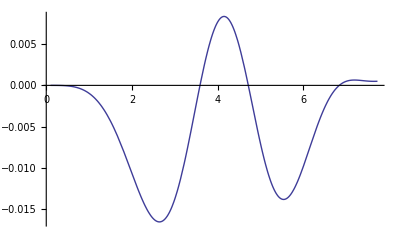

```mathematica
Plot[dur/.{a->-0.368462042449453,b->-2.073742707862413,c->-1.195962867077478,d1->-0.03562562381328482,d2->-0.0219818382704016,d3->2.1756630145801164,d4->0.25088239019967556},{r,0.1,r2}]
```

```mathematica
durs=Simplify[Normal[Chop[Series[dur,{r,0,4}]]]]
```

(b^2 (-0.002874504328524452734038685+0.003055058085985487197258636 d1^2+d1 (-0.0099802992784300289254141382+0.074341961080034042205139778 d2)-0.011176153828475588361269703 d2+0.17662430673125705531345381 d2^2)+b c ((0.0015321095414914627426906301+0.0041244944901594467466876313 d1+0.0088374302531804732732973746 d2) d3+(0.0053551876423082792334421913+0.025408840834893856362735668 d1+0.074859425128034029283731716 d2) d4)+c^2 (-0.00015838008621216655342050467 d3^2-0.00042014281368473868986984249 d3 d4+0.0030444021670422164391580576 d4^2)+a (b (0.005084228043414007226323794-0.0028780385654919313604060459 d1^2+d1 (0.008729436804082048772444565-0.066671492544345694745471192 d2)-0.01592453321781187717345968 d2-0.093531652044161696557293185 d2^2)+c ((-0.0019965242214518755648841117-0.0039930484429037511297682234 d1-0.005989572664355626694652335 d2) d3+(-0.011793310349142616761077641-0.023586620698285233522155281 d1-0.035379931047427850283232922 d2) d4))) r^4

```mathematica
dur1=Interpolation[Table[{r,If[r<0.1,durs,dur]},{r,0,r2+1,0.01}]]
```

InterpolatingFunction[{{0.,8.72}},<>]

```mathematica
w1=FullSimplify[Integrate[dur1[r],{r,0,r2}]]
```

0.+a^2 (0.00522151+0.0607204 d1^2+d1 (0.0182755+0.165693 d2)+(0.0240091+0.171019 d2) d2)+b^2 (-0.00215236+0.0593597 d1^2+d1 (0.02511+0.153113 d2)+(0.0332422+0.257312 d2) d2)+b c ((-0.00378427-0.00266428 d1+0.000699749 d2) d3+(-0.0324964-0.077976 d1+0.0489675 d2) d4)+c^2 (0.00154213 d3^2+0.00585223 d3 d4+0.0949142 d4^2)+a (b (-0.010443-0.121441 d1^2+d1 (-0.036551-0.331385 d2)+(-0.0480182-0.342038 d2) d2)+c ((0.00260714+0.00327766 d1+0.0046047 d2) d3+(0.00621254+0.0833668 d1+0.107557 d2) d4))

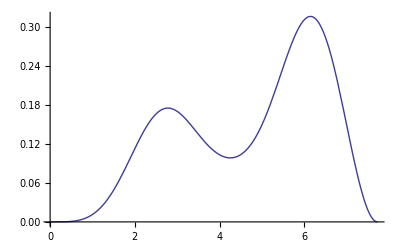

```mathematica
Plot[A1int/.{a->-0.368462042449453,b->-2.073742707862413,c->-1.195962867077478,d1->-0.03562562381328482,d2->-0.0219818382704016,d3->2.1756630145801164,d4->0.25088239019967556},{r,0.01,r2}]
```

```mathematica
Am1=Interpolation[Table[{r,A1int},{r,0.01,r2+1,0.01}]]
```

InterpolatingFunction[{{0.01,8.72}},<>]

```mathematica
Am=FullSimplify[Integrate[Am1[r],{r,0.1,r2}]]
```

0.+a^2 (0.710686+0.525217 d1^2+d1 (-0.175078+0.317214 d2)+(-0.370938+0.634327 d2) d2)+b^2 (0.415973+0.467874 d1^2+d1 (0.103694+0.285496 d2)+d2 (-0.785764+1.45343 d2))+b c ((-0.208923-0.00875538 d1+0.189703 d2) d3+(-0.287541-0.117477 d1+0.459626 d2) d4)+c^2 (0.0591751 d3^2+0.0824634 d3 d4+0.232965 d4^2)+a (b (-0.262959-0.79838 d1^2+d1 (-0.744235+0.399339 d2)+(-1.07084-0.246755 d2) d2)+c ((0.0630593+0.0792772 d1+0.111375 d2) d3+(0.0166959+0.224045 d1+0.289055 d2) d4))

```mathematica
Minimize[{w1,Am==1},{a,b,c,d1,d2,d3,d4}]
```

{-0.0341123,{a→-0.368462,b→-2.07374,c→-1.19596,d1→-0.0356256,d2→-0.0219818,d3→2.17566,d4→0.250882}}

#### Results

In the case n=2, we indeed find perturbations that lead to negative potential energy.

Here’s a slice of the equilibrium field l=1, m=0, n=2 (streamlines indicate direction of magnetic field in the plane and color represents the component perpendicular to the plane). The boundary is located at the second zero of the first spherical Bessel J function R=7.72525.

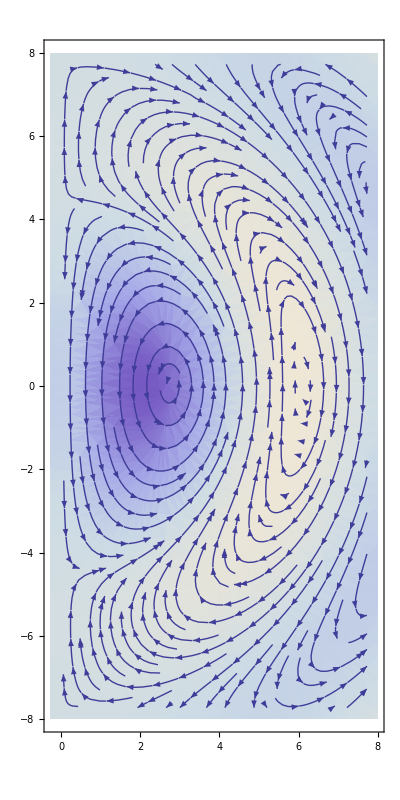

Here’s the displacement that minimizes δW and gives a negative δW:

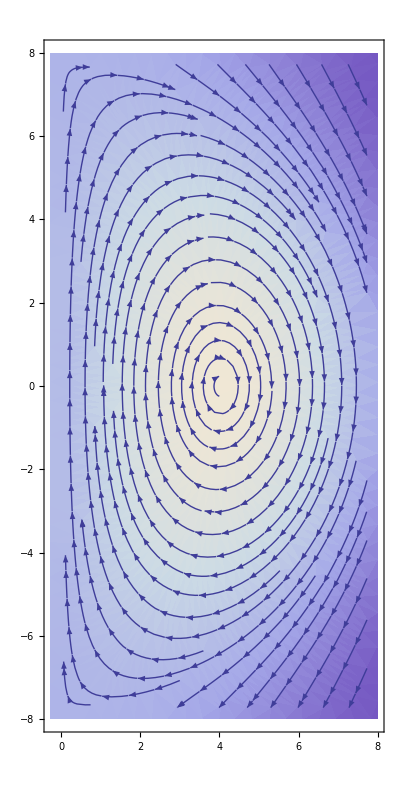

This is the first order perturbation to the magnetic field given by (B⃗)_1=∇×(ξ⃗×B⃗):

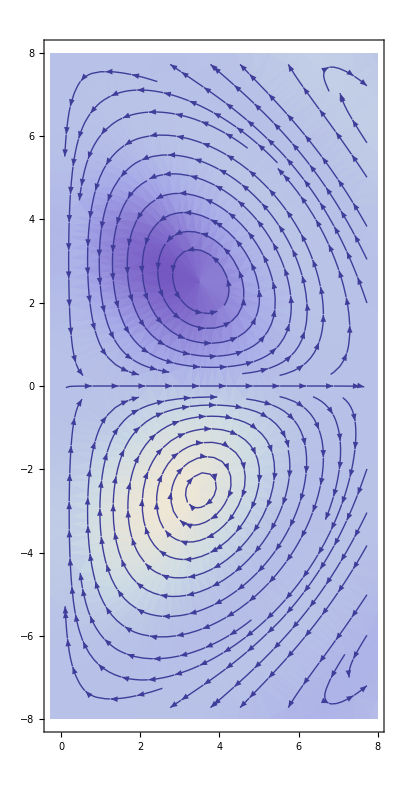

This looks very much like the force-free solution with l=2, m=0, n=1. If we look at the term diagram below, it seems not hard to understand the instability: since for a given helicity and radius, l=l, m=0, n=2 has higher energy than l=2, m=0, n=1, mixing in the latter will help reduce the total energy. I believe similar thing can happen to all n>1 solutions. Now the question is whether those n=1 solutions are stable. If the above logic is right, then to make them unstable, we have to find some displacement ξ that gives a perturbation (B⃗)_1=∇×(ξ⃗×B⃗) of lower l than B itself. This seems not likely to me but I still need to check.

## Energy levels

If we require a fixed, spherical boundary with radius R (fixed), and the helicity H is a fixed constant, then the energy E is decided by λ: E=λH. Here is an energy level diagram for this situation. The energy levels are degenerate in m.

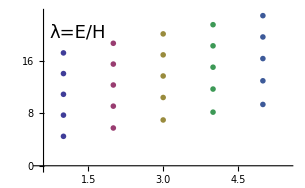

## Possible setup for numerical simulations

We might just consider the spherical, fixed, perfectly conducting boundary at the moment.

1. A very interesting case is the l=1, m=0, n=2 solution as mentioned above, i.e.

```mathematica
B[r_,θ_,ϕ_]:={(√(3/π) Cos[θ] (r Cos[r]-Sin[r]))/r^3,(√(3/π) (r Cos[r]+(-1+r^2) Sin[r]) Sin[θ])/(2 r^3),(√(3/π) (r Cos[r]-Sin[r]) Sin[θ])/(2 r^2)}
```

and the boundary is at

```mathematica
r2=BesselJZero[1+1/2,2]//N
```

7.72525

The above expression is in spherical coordinate representation. In Cartesian coordinate, a transformation can be performed to get the corresponding B:

```mathematica
MatrixForm[R=({{Sin[θ] Cos[ϕ], Cos [θ]Cos [ϕ], -Sin [ϕ]}, {Sin [θ] Sin [ϕ], Cos [θ] Sin [ϕ], Cos [ϕ]}, {Cos [θ], -Sin [θ], 0}})]
```

(Cos[ϕ] Sin[θ] | Cos[θ] Cos[ϕ] | -Sin[ϕ]
Sin[θ] Sin[ϕ] | Cos[θ] Sin[ϕ] | Cos[ϕ]
Cos[θ] | -Sin[θ] | 0)

```mathematica
MatrixForm[R1=Simplify[Inverse[R]]]
```

(Cos[ϕ] Sin[θ] | Sin[θ] Sin[ϕ] | Cos[θ]
Cos[θ] Cos[ϕ] | Cos[θ] Sin[ϕ] | -Sin[θ]
-Sin[ϕ] | Cos[ϕ] | 0)

```mathematica
Bc=FullSimplify[R.B[r,θ,ϕ]/.{r->√(x^2+y^2+z^2), θ->ArcCos[ z/(√(x^2+y^2+z^2))],ϕ->ArcTan[x,y]},Assumptions->Element[{x,y,z},Reals]]
```

{1/(2 (x^2+y^2+z^2)^(5/2))√(3/π) √(x^2+y^2) (-√(x^2+y^2+z^2) Cos[√(x^2+y^2+z^2)] (-3 z Cos[ArcTan[x,y]]+(x^2+y^2+z^2) Sin[ArcTan[x,y]])+Sin[√(x^2+y^2+z^2)] (z (-3+x^2+y^2+z^2) Cos[ArcTan[x,y]]+(x^2+y^2+z^2) Sin[ArcTan[x,y]])),1/(2 (x^2+y^2+z^2)^(5/2))√(3/π) √(x^2+y^2) (√(x^2+y^2+z^2) Cos[√(x^2+y^2+z^2)] ((x^2+y^2+z^2) Cos[ArcTan[x,y]]+3 z Sin[ArcTan[x,y]])+Sin[√(x^2+y^2+z^2)] (-(x^2+y^2+z^2) Cos[ArcTan[x,y]]+z (-3+x^2+y^2+z^2) Sin[ArcTan[x,y]])),-1/(2 (x^2+y^2+z^2)^(5/2))√(3/π) ((x^2+y^2-2 z^2) √(x^2+y^2+z^2) Cos[√(x^2+y^2+z^2)]+(x^4+2 z^2+y^2 (-1+y^2+z^2)+x^2 (-1+2 y^2+z^2)) Sin[√(x^2+y^2+z^2)])}

```mathematica
FullSimplify[Bc/.{ Cos[ArcTan[x,y]]->x/(√(x^2+y^2)),Sin[ArcTan[x,y]]->y/(√(x^2+y^2))}]
```

{1/(2 (x^2+y^2+z^2)^(5/2))√(3/π) (-√(x^2+y^2+z^2) (x^2 y+y^3-3 x z+y z^2) Cos[√(x^2+y^2+z^2)]+(x^2 y+x^3 z+x z (-3+y^2+z^2)+y (y^2+z^2)) Sin[√(x^2+y^2+z^2)]),1/(2 (x^2+y^2+z^2)^(5/2))√(3/π) (√(x^2+y^2+z^2) (x^3+3 y z+x (y^2+z^2)) Cos[√(x^2+y^2+z^2)]-(x^3-x^2 y z-y z (-3+y^2+z^2)+x (y^2+z^2)) Sin[√(x^2+y^2+z^2)]),-1/(2 (x^2+y^2+z^2)^(5/2))√(3/π) ((x^2+y^2-2 z^2) √(x^2+y^2+z^2) Cos[√(x^2+y^2+z^2)]+(x^4+2 z^2+y^2 (-1+y^2+z^2)+x^2 (-1+2 y^2+z^2)) Sin[√(x^2+y^2+z^2)])}

2. I believe the l=1, m=0, n=1 solution should be stable under any perturbations. It might be helpful to test this.

3. l=2, m=0, n=1 solution should be stable under ideal perturbations but probably unstable if reconnection can happen. This point is something I’m not sure and I really hope to know what can happen.